# AudioSpectralMap Example

Get Example Audio

```mathematica
fvoice = ExampleData[{"Audio","FemaleVoice"}];
```

```mathematica
fvSpk=Spectrogram[fvoice];
```

We can use the Piecewise function to selectively change values in the ShortTimeFourier data

```mathematica
?Piecewise
```

```mathematica
modified =AudioSpectralMap[Piecewise[
(* square frequencies between 1000 and 2000 HZ from 0 sec to 1 sec*)
{
{#Value 2,(0<#Time<1)∧(0<#Frequency<1000)},
(* cube all frequencies between from 1 sec to 1 sec*)
{#Value 4,(1<#Time<2)∧(1000<#Frequency<2000)},
{#Value 8,(2<#Time< 3)∧(2000<#Frequency<3000)},
{#Value 10,(3<#Time< 4)∧(3000<#Frequency<4000)},
{(#Value)^2,(3<#Time< 4)∧(4000<#Frequency<5000)}
}
]&,
fvoice
];
```

```mathematica
mdSpk=Spectrogram[modified,PlotRange->{0,5000}];
```

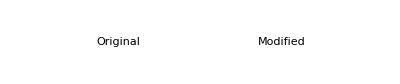

```mathematica
GraphicsRow[{Labeled[fvSpk,"Original"],Labeled[mdSpk,"Modified"]}]
```